### Estrela et al (2021) Functional attractors in microbial community assembly. Script to obtain the equations of probability distribution of mixed Gaussian for Alcaligenes and Pseudomonas at equilibrium and the equations for the potentials (U_A and U_P) to be used in Figures 2C and 2D.

note: Distribution parameters for each Gaussian (lambda, mu, and sigma) were obtained from mixture distribution of 2 gaussians (normalmixEM in R) for log10 relative abundance of A (or P) at Transfer 18 for all treatments. See companion R script.

### Analysis for Alcaligenes

#### Get equation for probability distribution

```mathematica
(*Params*)
l1=0.322185;
l2=0.677815;
mu1=-3.006816;
mu2=-0.590556;
sig1=0.458526;
sig2=0.122182;

DmixedG=MixtureDistribution[{l1,l2},{NormalDistribution[mu1,sig1],NormalDistribution[mu2,sig2]}];
mixedGAlc=PDF[DmixedG,x];
mixedGAlc
```

2.21317 ⅇ^(-33.4931 (0.590556+x)^2)+0.280318 ⅇ^(-2.37817 (3.00682+x)^2)

```mathematica
(*2.2131661111317307 ⅇ^(-33.49311531236609 (0.590556+x)^2)+0.280318277722824 ⅇ^(-2.3781654804426053 (3.006816+x)^2)*)
```

```mathematica
pAlc=Plot[mixedGAlc,{x,-4.5,0},Filling->Axis,AxesLabel->{"A","P(A)"}, PlotRange->{{-4.5, 0},{0,2.4}}]
```

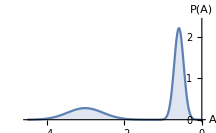

```mathematica
FindMinimum[mixedGAlc,{x,mu1,mu2}]
```

{0.000119615,{x→-1.17738}}

```mathematica
(*{0.00011961471074860016,{x->-1.1773766681068363}}*)
```

#### Get potential

```mathematica
potUAlc=(-Log[mixedGAlc]/2)
```

-1/2 Log[2.21317 ⅇ^(-33.4931 (0.590556+x)^2)+0.280318 ⅇ^(-2.37817 (3.00682+x)^2)]

```mathematica
(*potUAlc= (-1/2 Log[2.2131661111317307 ⅇ^(-33.49311531236609 (0.590556+x)^2)+0.280318277722824 ⅇ^(-2.3781654804426053 (3.006816+x)^2)])*)
```

```mathematica
Plot[potUAlc,{x,-5,0}]
```

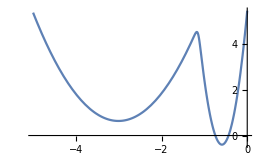

```mathematica
potUAlcd=D[(-Log[mixedGAlc]/2),x]
```

-(-148.252 ⅇ^(-33.4931 (0.590556+x)^2) (0.590556+x)-1.33329 ⅇ^(-2.37817 (3.00682+x)^2) (3.00682+x))/(2 (2.21317 ⅇ^(-33.4931 (0.590556+x)^2)+0.280318 ⅇ^(-2.37817 (3.00682+x)^2)))

```mathematica
(*-(-148.25165553111177 ⅇ^(-33.49311531236609 (0.590556+x)^2) (0.590556+x)-1.333286503235087 ⅇ^(-2.3781654804426053 (3.006816+x)^2) (3.006816+x))/(2 (2.2131661111317307 ⅇ^(-33.49311531236609 (0.590556+x)^2)+0.280318277722824 ⅇ^(-2.3781654804426053 (3.006816+x)^2)))*)
```

```mathematica
Plot[potUAlcd,{x,-5,0},AxesLabel->{x,Ud}]
```

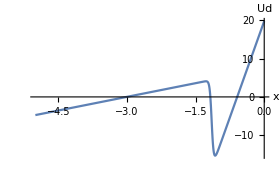

```mathematica
FindRoot[potUAlcd,{x,-0.5}]
```

{x→-0.590556}

```mathematica
(*{x->-0.5905560202823228}*)
```

```mathematica
FindRoot[potUAlcd,{x,-1.2}]
```

{x→-1.17738}

```mathematica
(*{x->-1.1773753326343022}*)
```

```mathematica
FindRoot[potUAlcd,{x,-3}]
```

{x→-3.00682}

```mathematica
(*{x->-3.006816}*)
```

### Analysis for Pseudomonas

#### Get equation for probability distribution

```mathematica
(*Params*)
l1=0.219607;
l2=0.780393;
mu1=-3.166490;
mu2=-1.082471;
sig1=0.744824;
sig2=0.274493;

DmixedG=MixtureDistribution[{l1,l2},{NormalDistribution[mu1,sig1],NormalDistribution[mu2,sig2]}];
mixedGPseu=PDF[DmixedG,x]
```

1.13421 ⅇ^(-6.63602 (1.08247+x)^2)+0.117626 ⅇ^(-0.901286 (3.16649+x)^2)

```mathematica
(*1.134206566394463 ⅇ^(-6.636016494785681 (1.082471+x)^2)+0.11762579800344436 ⅇ^(-0.9012861138728224 (3.16649+x)^2)*)
```

```mathematica
pPseu=Plot[mixedGPseu,{x,-4.5,0},Filling->Axis,AxesLabel->{"P","Pd(P)"}]
```

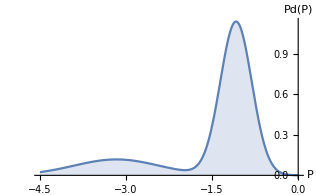

```mathematica
FindMinimum[mixedGPseu,{x,mu1,mu2}]
```

{0.0384568,{x→-1.97225}}

```mathematica
(*{0.03845682242457371,{x->-1.972247766726776}}*)
```

#### Get potential

```mathematica
potUPseu=(-Log[mixedGPseu]/2)
```

-1/2 Log[1.13421 ⅇ^(-6.63602 (1.08247+x)^2)+0.117626 ⅇ^(-0.901286 (3.16649+x)^2)]

```mathematica
(*potUPseu= (-1/2 Log[1.134206566394463 ⅇ^(-6.636016494785681 (1.082471+x)^2)+0.11762579800344436 ⅇ^(-0.9012861138728224 (3.16649+x)^2)])*)
```

```mathematica
Plot[potUPseu,{x,-5,0}]
```

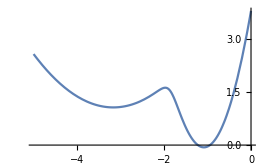

```mathematica
potUPseud=D[(-Log[mixedGPseu]/2),x]
```

-(-15.0532 ⅇ^(-6.63602 (1.08247+x)^2) (1.08247+x)-0.212029 ⅇ^(-0.901286 (3.16649+x)^2) (3.16649+x))/(2 (1.13421 ⅇ^(-6.63602 (1.08247+x)^2)+0.117626 ⅇ^(-0.901286 (3.16649+x)^2)))

```mathematica
(*-(-15.053226966175773 ⅇ^(-6.636016494785681 (1.082471+x)^2) (1.082471+x)-0.21202899674742792 ⅇ^(-0.9012861138728224 (3.16649+x)^2) (3.16649+x))/(2 (1.134206566394463 ⅇ^(-6.636016494785681 (1.082471+x)^2)+0.11762579800344436 ⅇ^(-0.9012861138728224 (3.16649+x)^2)))
*)
```

```mathematica
Plot[potUPseud,{x,-5,0}]
```

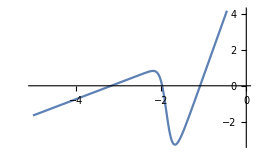

```mathematica
FindRoot[potUPseud,{x,0}]
```

{x→-1.08306}

```mathematica
(*{x->-1.0830578102450865}*)
```

```mathematica
FindRoot[potUPseud,{x,-2}]
```

{x→-1.97225}

```mathematica
(*{x->-1.972248039555942}*)
```

```mathematica
FindRoot[potUPseud,{x,-3}]
```

{x→-3.16649}

```mathematica
(*{x->-3.1664899999549925}*)
```